## circular mot coil, 4.79117 G/cm / A

4.79117 i

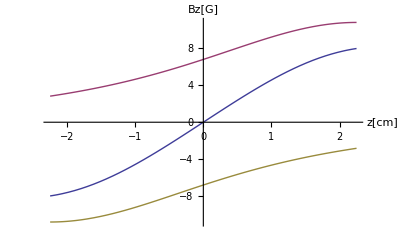

```mathematica
Clear["Global`*"]

μ0=4π 10^-7;
ID=66.802;
OD=82.85;
n=8 8;
R = (ID+OD)/4 10^-3;
d=0.045;

(*in cgs units*)

Bz1=10^4 n μ0/(4π)(2 π R^2 i)/(((z/100-d/2)^2+R^2)^(3/2));

Bz2=-10^4 n μ0/(4π)(2 π R^2 i)/(((z/100+d/2)^2+R^2)^(3/2));
D[(Bz1+Bz2), z]/.z->0
i=1;
Plot[{Bz1+Bz2,Bz1,Bz2},{z,-100d/2,100d/2},AxesLabel->{"z[cm]","Bz[G]"}]
```

## 1 MHz/G * 4.8 G/cm/A * 1 cm * 1 A

## energy shift of 4, 4 -> 5, 5 state * MOT coil transfer function * generous MOT size * 1 A MOT current = 5 MHz

## if the mot current fluctuates by 1mA you get a 5 kHz energy shift.